```mathematica
FullSimplify[Integrate[(1+x)LegendreP[l,x],{x,-1,1}],Assumptions->l∈Integers]
```

0

```mathematica
FullSimplify[(2 Sin[l π])/((l+l^2) π),Assumptions->l∈Integers]
```

0

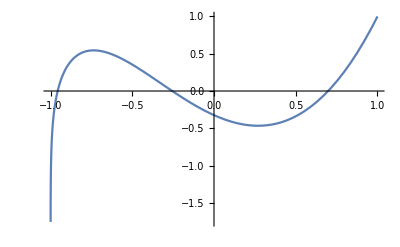

```mathematica
Plot[LegendreP[2.5,x],{x,-1,1}]
```

```mathematica
Integrate[(1+x)^2 LegendreP[l,x],{x,-1,1}]
```

(32 Sin[l π])/((-2+l) (-1+l) l (1+l) (2+l) (3+l) π)

```mathematica
Integrate[((R-rp)rp(1-x)^2)/(√(1-2 r/rp x+(r/rp)^2)),{rp,0,R},{x,-1,1},{ϕ,0,2Pi},Assumptions->rp>0&&r>0&&R>0&&Im[rp]==0&&Im[R]==0&&Im[r]]
```

```mathematica
Factor[-1/(225 r^3)π (-10 r^6-77 r^5 R+150 r^4 R^2-100 r^3 R^3-50 r^2 R^4+15 r R^5-2 R^6+120 r^5 R Log[r]-60 r^5 R Log[R]+1/(r-R)Abs[r-R] (10 r^6+77 r^5 R-150 r^4 R^2+100 r^3 R^3-50 r^2 R^4+15 r R^5-2 R^6+60 r^5 R Log[R]))]
```

1/(225 r^3 (r-R))π (10 r^7+67 r^6 R-227 r^5 R^2+250 r^4 R^3-50 r^3 R^4-65 r^2 R^5+17 r R^6-2 R^7-10 r^6 Abs[r-R]-77 r^5 R Abs[r-R]+150 r^4 R^2 Abs[r-R]-100 r^3 R^3 Abs[r-R]+50 r^2 R^4 Abs[r-R]-15 r R^5 Abs[r-R]+2 R^6 Abs[r-R]-120 r^6 R Log[r]+120 r^5 R^2 Log[r]+60 r^6 R Log[R]-60 r^5 R^2 Log[R]-60 r^5 R Abs[r-R] Log[R])

```mathematica
FullSimplify[∫_0^R -2 π rp (-R+rp) Abs[rp] If[(Re[r]<0&&((R>rp&&(0<rp≤-Re[r]||(rp+Re[r]>0&&-√(rp^2-Re[r]^2)≤Im[r]≤√(rp^2-Re[r]^2))))||(R<rp&&(Re[r]≤rp<0||(-√(rp^2-Re[r]^2)≤Im[r]≤√(rp^2-Re[r]^2)&&rp<Re[r])))))||Re[r]==0||(Re[r]>0&&((rp+Re[r]==0&&R+Re[r]<0)||(R>rp&&(0<rp≤Re[r]||(rp>Re[r]&&-√(rp^2-Re[r]^2)≤Im[r]≤√(rp^2-Re[r]^2))))||(R<rp&&(-Re[r]<rp<0||(-√(rp^2-Re[r]^2)≤Im[r]≤√(rp^2-Re[r]^2)&&rp+Re[r]<0))))),-1/(15 r^3 rp^3)2 (2 r^2 rp^2 (3 √((r-rp)^2)-8 √((r+rp)^2))-2 r rp^3 (2 √((r-rp)^2)-3 √((r+rp)^2))+r^4 (√((r-rp)^2)-√((r+rp)^2))+rp^4 (√((r-rp)^2)-√((r+rp)^2))+2 r^3 rp (-2 √((r-rp)^2)+3 √((r+rp)^2))),Integrate[(-1+x)^2/(√(r^2+rp^2-2 r rp x)),{x,-1,1},Assumptions->Re[r]≠0&&(((Re[R]<0&&Im[R]==0)&&(Re[R]<rp&&Im[R]==0)&&(Re[rp]<0&&Im[rp]==0)&&((R+Re[r]≥0&&((Re[r]>0&&(rp+Re[r]==0||(rp+Re[r]<0&&(√(rp^2-Re[r]^2)<Im[r]||Im[r]+√(rp^2-Re[r]^2)<0))))||((Re[rp]<Re[r]&&Im[rp]==0)&&rp+Re[r]≤0&&(√(rp^2-Re[r]^2)<Im[r]||Im[r]+√(rp^2-Re[r]^2)<0))))||(((Re[rp]<Re[r]&&Im[rp]==0)||Re[r]≥0)&&(Re[r]<0||rp+Re[r]<0)&&(√(rp^2-Re[r]^2)<Im[r]||Im[r]+√(rp^2-Re[r]^2)<0))))||((Re[R]>0&&Im[R]==0)&&(Re[R]>rp&&Im[R]==0)&&(Re[rp]>0&&Im[rp]==0)&&(√(rp^2-Re[r]^2)<Im[r]||Im[r]+√(rp^2-Re[r]^2)<0)&&(rp+Re[r]≠0||R+Re[r]≥0)&&(Re[r]≥0||rp+Re[r]>0)&&(Re[r]<0||(Re[rp]>Re[r]&&Im[rp]==0))))]]ⅆrp,Assumptions->rp>0&&r>0&&R>0&&Im[rp]==0&&Im[R]==0&&Im[r]==0]
```

∫_0^R 2 π (R-rp) rp^2 If[R>rp&&(r≥rp||√(-r^2+rp^2)≥0),-1/(15 r^3 rp^3)2 (2 r^2 rp^2 (3 √((r-rp)^2)-8 √((r+rp)^2))-2 r rp^3 (2 √((r-rp)^2)-3 √((r+rp)^2))+r^4 (√((r-rp)^2)-√((r+rp)^2))+rp^4 (√((r-rp)^2)-√((r+rp)^2))+2 r^3 rp (-2 √((r-rp)^2)+3 √((r+rp)^2))),Integrate[(-1+x)^2/(√(r^2+rp^2-2 r rp x)),{x,-1,1},Assumptions→Re[r]≠0&&(((Re[R]<0&&Im[R]==0)&&(Re[R]<rp&&Im[R]==0)&&(Re[rp]<0&&Im[rp]==0)&&((R+Re[r]≥0&&((Re[r]>0&&(rp+Re[r]==0||(rp+Re[r]<0&&(√(rp^2-Re[r]^2)<Im[r]||Im[r]+√(rp^2-Re[r]^2)<0))))||((Re[rp]<Re[r]&&Im[rp]==0)&&rp+Re[r]≤0&&(√(rp^2-Re[r]^2)<Im[r]||Im[r]+√(rp^2-Re[r]^2)<0))))||(((Re[rp]<Re[r]&&Im[rp]==0)||Re[r]≥0)&&(Re[r]<0||rp+Re[r]<0)&&(√(rp^2-Re[r]^2)<Im[r]||Im[r]+√(rp^2-Re[r]^2)<0))))||((Re[R]>0&&Im[R]==0)&&(Re[R]>rp&&Im[R]==0)&&(Re[rp]>0&&Im[rp]==0)&&(√(rp^2-Re[r]^2)<Im[r]||Im[r]+√(rp^2-Re[r]^2)<0)&&(rp+Re[r]≠0||R+Re[r]≥0)&&(Re[r]≥0||rp+Re[r]>0)&&(Re[r]<0||(Re[rp]>Re[r]&&Im[rp]==0))))]]ⅆrp

```mathematica
FourierTransform[Sin[a t],t,ω,FourierParameters->{-1, 1}]
```

1/2 ⅈ DiracDelta[-a+ω]-1/2 ⅈ DiracDelta[a+ω]

```mathematica
exp[a_+b_]:=exp[a]exp[b]
```

```mathematica
exp[a]
```

```mathematica
FullSimplify[Integrate[x^2 LegendreP[λ,x],{x,-1,1}],Assumptions->λ∈Integers]
```

0

```mathematica
Integrate[1/R^e,R]
```

```mathematica
f[R_]:=R^(1-e)/(1-e);
```

```mathematica
f[r2]-f[r1]
```

-r1^(1-e)/(1-e)+r2^(1-e)/(1-e)

```mathematica
Series[R^(1-e),{e,0,1}]
```

R-R Log[R] e+O[e]^2

```mathematica
LegendreP[2,x]
```

1/2 (-1+3 x^2)

```mathematica
(2π β Integrate[rp^2(R-rp)(rp/r-4/3(rp/r)^2),rp])
```

```mathematica
f[rp_]:=(π rp^4 (9 r (5 R-4 rp)+8 rp (-6 R+5 rp)) β)/(90 r^2)
```

```mathematica
(f[r]-f[0])//Simplify
```

1/90 π r^3 (4 r-3 R) β

```mathematica
2 π (r^4/45-(r^3 R)/60) β//Simplify
(2 π (r^4/45-(r^3 R)/60) β/.r->R)//Simplify
```

1/90 π r^3 (4 r-3 R) β

1/90 π R^4 β

```mathematica
((1/6 ra ((a-R) (3 a-3 R-8 ra)-8 R ra Log[R/a]))//Simplify)/.{r->s,ra->r}
```

1/6 r ((3 a-8 r-3 R) (a-R)-8 r R Log[R/a])

```mathematica
-1/3 ra ((3 r^2)/2+r (-3 R-4 ra))/.{r->s}
```

-1/3 ra ((-3 R-4 ra) s+(3 s^2)/2)

```mathematica
Log[-Infinity]
```

∞

```mathematica
β Integrate[R^-ϵ,R]
```

```mathematica
(r1 r2)^-ϵ (-r1^ϵ r2+r1 r2^ϵ) β==r2^(1-ϵ) β-r1^(1-ϵ) β//Reduce
```

Reduce::useq: The answer found by Reduce contains unsolved equation(s) {0==1-2}. A likely reason for this is that the solution set depends on branch cuts of Wolfram Language functions.

(C[1]∈ℤ&&r1 r2≠0&&Log[r1]+Log[r2]-Log[r1 r2]≠0&&ϵ==-(ⅈ π (1+2 C[1]))/(Log[r1]+Log[r2]-Log[r1 r2]))||(Re[r1]<0&&r2==r1)||(Im[r1]≠0&&Re[r1]==0&&r2==r1)||(Re[r1]>0&&r2==r1)||((C[1]|C[2])∈ℤ&&r1≠0&&r2≠0&&Log[r1]-Log[r2]≠0&&0==C[1]-C[2]&&ϵ==(2 ⅈ π C[1]+Log[r1/r2])/(Log[r1]-Log[r2]))||(r1 r2≠0&&β==0)

```mathematica
Solve[((r1 r2)^-ϵ (-r1^ϵ r2+r1 r2^ϵ) β)/(-1+ϵ)==-(r1^(1-ϵ) β)/(1-ϵ)+(r2^(1-ϵ) β)/(1-ϵ),{r1,r2,β,ϵ},Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[((r1 r2)^-ϵ (-r1^ϵ r2+r1 r2^ϵ) β)/(-1+ϵ)==-(r1^(1-ϵ) β)/(1-ϵ)+(r2^(1-ϵ) β)/(1-ϵ),{r1,r2,β,ϵ},ℝ]

```mathematica
ConditionalExpression[((r1 r2)^-ϵ (-r1^ϵ r2+r1 r2^ϵ) β)/(-1+ϵ), r1≠r2]
```

```mathematica
Series[r^(1-e),{e,0,1}]
```

r-r Log[r] e+O[e]^2

```mathematica
Solve[α[b] Qa/b((a+b)(1-Log[a+b])-(b-a)(1-Log[b-a]))==α]
```

```mathematica
FourierTransform[x^3 Exp[-I a x],x,k]
```

ⅈ √(2 π) DiracDelta^(3)[-a+k]

```mathematica
(-1)^n(I)^-n
```

(-1)^n ⅈ^-n

```mathematica
Simplify[(-1)^n ⅈ^-n]
```

ⅈ^n

```mathematica
6./31
```

0.193548